#### 10.04.21 - Расчёт ошибки кумулянта прямоугольного Изинга при разных отношениях сторон

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data = Import["results.txt", "table"]
```

{{50,0.25,1,0.109901,0.00462847,0.0279148,0.00212686,0.229605},{50,0.5,1,0.141223,0.00422358,0.0374659,0.00187789,0.373811},{50,0.75,1,0.143292,0.0042087,0.0377988,0.00180791,0.386359},{100,0.25,1,0.0890685,0.00405307,0.018081,0.00161062,0.240281},{100,0.5,1,0.115757,0.00358826,0.0261556,0.00130813,0.349347},{100,0.75,1,0.118994,0.00358253,0.0265074,0.00162272,0.375988}}

data[...][1] - L
data[...][2] - CoefXY
data[...][3] - OpenBorderQ (1 - Yes, 0 - No)
data[...][4] - ⟨m2⟩
data[...][5] - σ(m2)
data[...][6] - ⟨m4⟩
data[...][7] - σ(m4)
data[...][8] - U_4

#### Реализация расчёта ошибки:

1. Генерация набора из 1000 значений намагниченностей (второй и четвёртой степени) (средним в распределении является средняя намагниченность, а С.К.О. - её ошибка) и набора кумулянтов из первых двух наборов

```mathematica
dM2 = RandomVariate[NormalDistribution[data[[1]][[4]], data[[1]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[data[[1]][[6]], data[[1]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
```

Так выглядит гистограмма распределения кумулянта

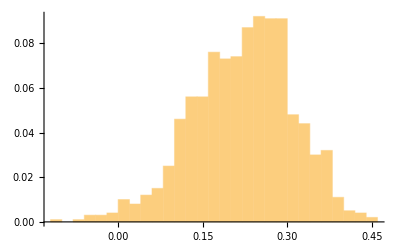

```mathematica
Histogram[dU4, Automatic, "Probability"]
```

На основе гистограммы задаём распределение кумулянта и находит его отклонение

```mathematica
StandardDeviation[HistogramDistribution[dU4]]
```

0.0889934

#### Полуавтоматизированный алгоритм для задания набора точек и их ошибок:

```mathematica
Ls={50,100};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

#### График для первых шести расчётов (L=50, 100, AspectRatio=1/4, 1/2 3/4)

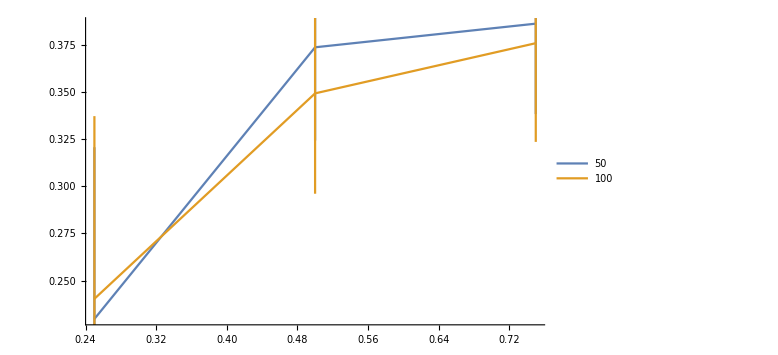

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->Large, Joined->True]
```

#### Как и ожидалось, погрешности слишком большие -> требуется увеличение времени работы алгоритма

#### 10.04.2021 - Расчёт при новых данных

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data=Import["results2.txt","table"]
```

{{50,0.25,1,0.109567,0.0012553,0.0277495,0.000555247,0.2295},{50,0.5,1,0.139515,0.00153194,0.0380324,0.000659079,0.348689},{50,0.75,1,0.143534,0.00168099,0.0379902,0.000750858,0.385329},{100,0.25,1,0.0873405,0.00117321,0.0177195,0.000429325,0.225718},{100,0.5,1,0.11418,0.00149426,0.0251839,0.000440689,0.356097},{100,0.75,1,0.120044,0.00115745,0.0260882,0.000407595,0.396548},{200,0.25,1,0.0725037,0.000832001,0.0118999,0.000244944,0.245425},{200,0.5,1,0.09441,0.00115648,0.0172971,0.000302764,0.353132},{400,0.25,1,0.0614871,0.000832213,0.00863458,0.000227393,0.238706},{200,0.75,1,0.0983118,0.000970211,0.0178971,0.00028873,0.382767},{400,0.5,1,0.0782073,0.000808983,0.0118324,0.000192356,0.355153},{400,0.75,1,0.0841728,0.000761902,0.0128747,0.000193869,0.394277},{}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Ls={50,100,200,400};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
FullData
```

{{{{0.25,0.2295},ErrorBar[0.0237283]},{{0.5,0.348689},ErrorBar[0.018332]},{{0.75,0.385329},ErrorBar[0.0194156]}},{{{0.25,0.225718},ErrorBar[0.0290121]},{{0.5,0.356097},ErrorBar[0.0204822]},{{0.75,0.396548},ErrorBar[0.0149492]}},{{{0.25,0.245425},ErrorBar[0.0231351]},{{0.5,0.353132},ErrorBar[0.0193881]},{{0.75,0.382767},ErrorBar[0.0161074]}},{{{0.25,0.238706},ErrorBar[0.0290816]},{{0.5,0.355153},ErrorBar[0.0167208]},{{0.75,0.394277},ErrorBar[0.0144576]}}}

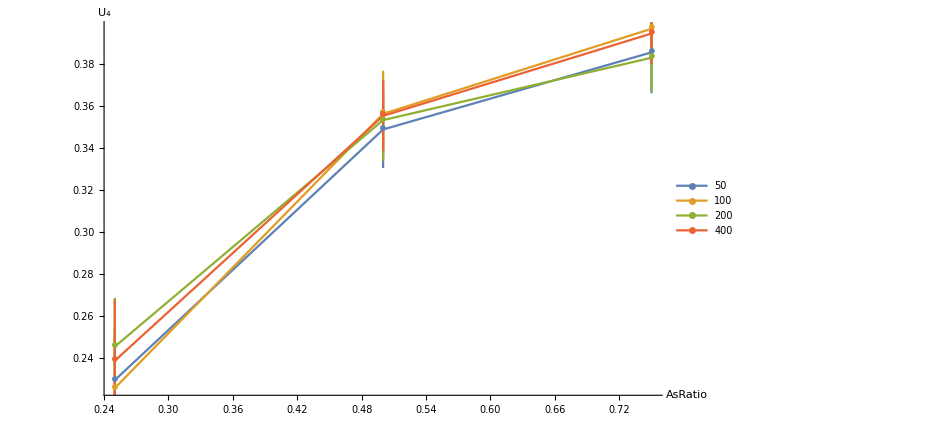

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["AsRatio",FontSize->16], Style["U_4",FontSize->16]}]
```

#### 12.04.2021 (Расчёт кумулянтов для модели с PBC)

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["resultsPBC.txt","table"]
```

{{50,0.125,0,0.215661,0.00240819,0.0995194,0.00179676,0.286747},{50,0.375,0,0.39827,0.0023668,0.211818,0.00176819,0.554871},{50,0.625,0,0.425001,0.00186156,0.215259,0.00146284,0.602755},{50,0.875,0,0.419661,0.00176121,0.20526,0.00131248,0.611505},{50,1,0,0.411456,0.00170725,0.197553,0.00139595,0.611031},{50,0.25,0,0.339491,0.00268587,0.180527,0.00197685,0.477888},{100,0.125,0,0.185932,0.00201219,0.0737009,0.00121518,0.28937},{50,0.5,0,0.424286,0.00277081,0.22089,0.00188826,0.590986},{100,0.25,0,0.289414,0.00248101,0.129659,0.00140714,0.484009},{50,0.75,0,0.419076,0.00180916,0.207595,0.00134077,0.605987},{200,0.125,0,0.158385,0.00173186,0.0528615,0.000893624,0.29759},{100,0.375,0,0.337111,0.00195343,0.150621,0.00121705,0.558207},{100,0.5,0,0.354643,0.00175949,0.155508,0.00113035,0.587857},{100,0.625,0,0.358134,0.00169111,0.153296,0.00111774,0.601601},{200,0.25,0,0.245588,0.00227325,0.0929741,0.00122646,0.486162},{100,0.75,0,0.354104,0.00173756,0.147622,0.00105541,0.607562},{400,0.125,0,0.133875,0.00171642,0.0371573,0.000760954,0.30893},{100,0.875,0,0.351626,0.00179054,0.144611,0.00107324,0.610132},{200,0.375,0,0.286042,0.00176048,0.10733,0.000935553,0.562739},{100,1,0,0.347614,0.00149502,0.140914,0.000925412,0.611278},{200,0.5,0,0.29897,0.0017138,0.11013,0.000885466,0.589294},{200,0.625,0,0.302599,0.00141217,0.109309,0.000782609,0.602077},{400,0.25,0,0.210144,0.00159144,0.0671965,0.000674728,0.492787},{200,0.75,0,0.30243,0.00125822,0.106679,0.000668264,0.611214},{200,0.875,0,0.296173,0.00145264,0.102818,0.000755462,0.609289},{200,1,0,0.292656,0.0014874,0.0995816,0.000737693,0.612436},{400,0.375,0,0.242891,0.00210325,0.0776168,0.000920871,0.561456},{400,0.5,0,0.253901,0.00154286,0.0788962,0.000585867,0.592052},{400,0.625,0,0.254844,0.00111635,0.077227,0.000503627,0.603632},{400,0.75,0,0.25115,0.00107139,0.0744048,0.000473549,0.606799},{400,0.875,0,0.252965,0.00112627,0.074379,0.000477704,0.612557},{400,1,0,0.247955,0.00100456,0.0713842,0.000519461,0.612978},{}}

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
DotsForPlot[data0_,Len_]:=Module[{data=data0,Ls=Len,FullData={},line={},dM2={},dM4={},dU4={},dot={},lData={}},
Needs["ErrorBarPlots`"];
Do[
lData=Sort[Select[data,#[[1]]==L&],#1[[2]]<#2[[2]]&];
	line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}];
Return[FullData];];
```

```mathematica
Ls={50,100,200,400};
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

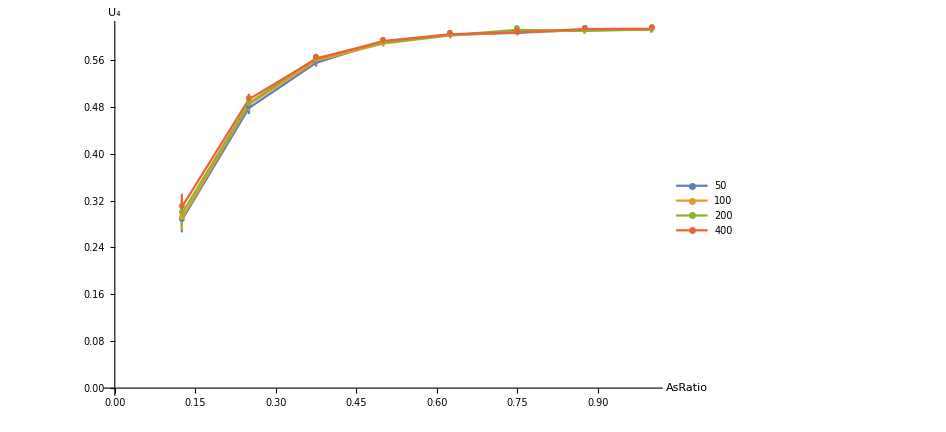

```mathematica
ErrorListPlot[DotsForPlot[data,Ls], PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["AsRatio",FontSize->16], Style["U_4",FontSize->16]}]
```

#### 14.04.2021 (Итоговые графики для обоих моделей) (Обновлено 17.04.2021)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["resultsALL.txt","table"];
```

```mathematica
Ls={50,100,200,400};
```

```mathematica
dataOBC=Select[data, #[[3]]==1&];
```

```mathematica
dataPBC=Select[data,#[[3]]==0&];
```

```mathematica
LinesOBC=DotsForPlot[dataOBC,Ls];
LinesPBC=DotsForPlot[dataPBC,Ls];
```

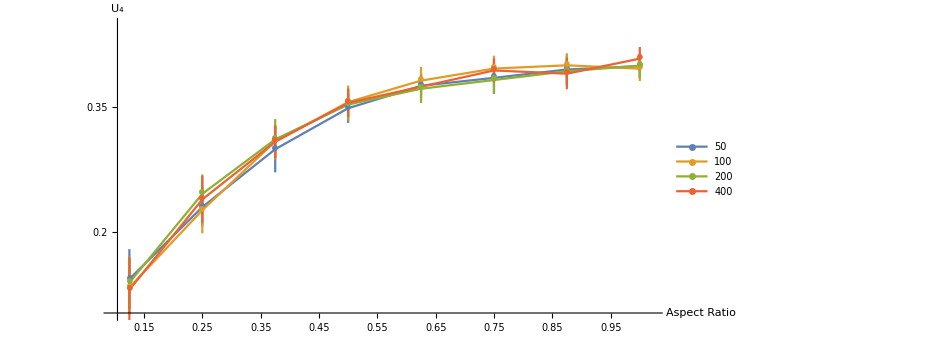

```mathematica
ErrorListPlot[LinesOBC, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["Aspect Ratio",FontSize->16], Style["U_4",FontSize->16]}, GridLines->{0.05*Range[20],0.05*Range[20]},Ticks->{0.05*Range[20],0.05*Range[20]},AspectRatio->0.5,PlotRange->{{0.1,1.02},{0.1,0.45}}]
```

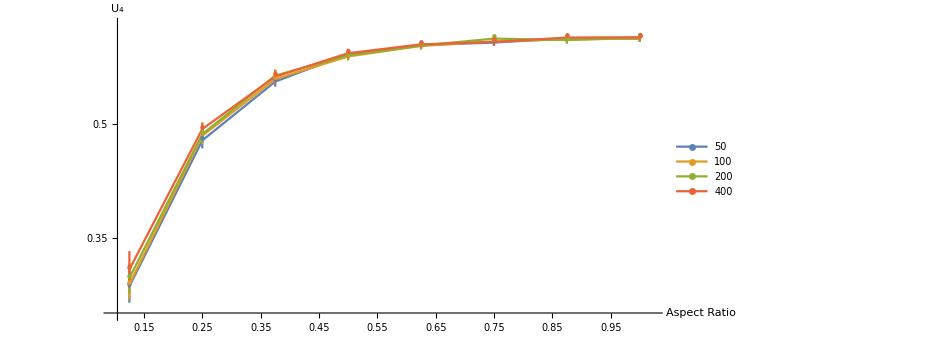

```mathematica
ErrorListPlot[LinesPBC, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,15}, AxesLabel->{Style["Aspect Ratio",FontSize->16], Style["U_4",FontSize->16]}, GridLines->{0.05*Range[20],0.05*Range[20]},Ticks->{0.05*Range[20],0.05*Range[20]},AspectRatio->0.5,PlotRange->{{0.1,1.02},{0.25,0.63}}]
```

Добавим точки одномерного Изинга (Проект6)

```mathematica
Needs["ErrorBarPlots`"];
LinesPBC={{{{0,0.0455262},ErrorBar[0]},{{0.125,0.286747},ErrorBar[0.021103206115027095]},{{0.25,0.477888},ErrorBar[0.0102751366576545]},{{0.375,0.554871},ErrorBar[0.006355869518278932]},{{0.5,0.590986},ErrorBar[0.006254942792220312]},{{0.625,0.602755},ErrorBar[0.004602476434793534]},{{0.75,0.605987},ErrorBar[0.0043996055883318945]},{{0.875,0.611505},ErrorBar[0.004177663142631407]},{{1,0.611031},ErrorBar[0.00416642632630888]}},{{{0,0.0227633},ErrorBar[0]},{{0.125,0.28937},ErrorBar[0.01947144340652084]},{{0.25,0.484009},ErrorBar[0.010443721000363351]},{{0.375,0.558207},ErrorBar[0.006006482276134177]},{{0.5,0.587857},ErrorBar[0.005008200209028693]},{{0.625,0.601601},ErrorBar[0.004931007334503564]},{{0.75,0.607562},ErrorBar[0.004916309320343678]},{{0.875,0.610132},ErrorBar[0.004823945411507207]},{{1,0.611278},ErrorBar[0.004187072047701209]}},{{{0,0.0113816},ErrorBar[0]},{{0.125,0.29759},ErrorBar[0.01886465765216365]},{{0.25,0.486162},ErrorBar[0.011812396384030008]},{{0.375,0.562739},ErrorBar[0.006886846690151305]},{{0.5,0.589294},ErrorBar[0.005692904121247137]},{{0.625,0.602077},ErrorBar[0.004705451023302477]},{{0.75,0.611214},ErrorBar[0.004049964485442316]},{{0.875,0.609289},ErrorBar[0.005059807242707085]},{{1,0.612436},ErrorBar[0.0048268301537754054]}},{{{0,0.00569082},ErrorBar[0]},{{0.125,0.30893},ErrorBar[0.023220933084898854]},{{0.25,0.492787},ErrorBar[0.009462795429122485]},{{0.375,0.561456},ErrorBar[0.008894737620272243]},{{0.5,0.592052},ErrorBar[0.00577970010757792]},{{0.625,0.603632},ErrorBar[0.004507553364359108]},{{0.75,0.606799},ErrorBar[0.00417317592885646]},{{0.875,0.612557},ErrorBar[0.004281640962647969]},{{1,0.612978},ErrorBar[0.004261951352743337]}}};
LinesOBC={{{{0,0.0448609},ErrorBar[0]},{{0.125,0.142698},ErrorBar[0.0387364277306687]},{{0.25,0.2295},ErrorBar[0.023467603911207634]},{{0.375,0.299275},ErrorBar[0.02761862475456292]},{{0.5,0.348689},ErrorBar[0.017822253177792496]},{{0.625,0.375821},ErrorBar[0.01575343877803633]},{{0.75,0.385329},ErrorBar[0.019745795333015636]},{{0.875,0.395412},ErrorBar[0.017841527634517233]},{{1,0.399503},ErrorBar[0.014658250520895737]}},{{{0,0.0226025},ErrorBar[0]},{{0.125,0.132452},ErrorBar[0.031075986441838538]},{{0.25,0.225718},ErrorBar[0.02816928173264828]},{{0.375,0.308687},ErrorBar[0.019136635893838252]},{{0.5,0.356097},ErrorBar[0.01996234726512354]},{{0.625,0.382013},ErrorBar[0.015966553583453932]},{{0.75,0.396548},ErrorBar[0.015078568676547546]},{{0.875,0.40049},ErrorBar[0.014537115715758393]},{{1,0.396412},ErrorBar[0.015430529262903312]}},{{{0,0.0113421},ErrorBar[0]},{{0.125,0.138382},ErrorBar[0.029917039180596294]},{{0.25,0.245425},ErrorBar[0.02235646960799807]},{{0.375,0.31116},ErrorBar[0.026021409134274757]},{{0.5,0.353132},ErrorBar[0.019773090510422087]},{{0.625,0.372229},ErrorBar[0.0166680332773049]},{{0.75,0.382767},ErrorBar[0.01603698641682248]},{{0.875,0.39333},ErrorBar[0.017088777262674593]},{{1,0.400006},ErrorBar[0.013988582248868005]}},{{{0,0.00568103},ErrorBar[0]},{{0.125,0.129828},ErrorBar[0.03828217905675338]},{{0.25,0.238706},ErrorBar[0.02861071361104703]},{{0.375,0.30833},ErrorBar[0.019678019039864342]},{{0.5,0.355153},ErrorBar[0.017099173469304722]},{{0.75,0.394277},ErrorBar[0.01399761527308514]},{{0.875,0.390363},ErrorBar[0.018932311885591403]},{{1,0.40851539},ErrorBar[0.014382048996349608]}}};
```

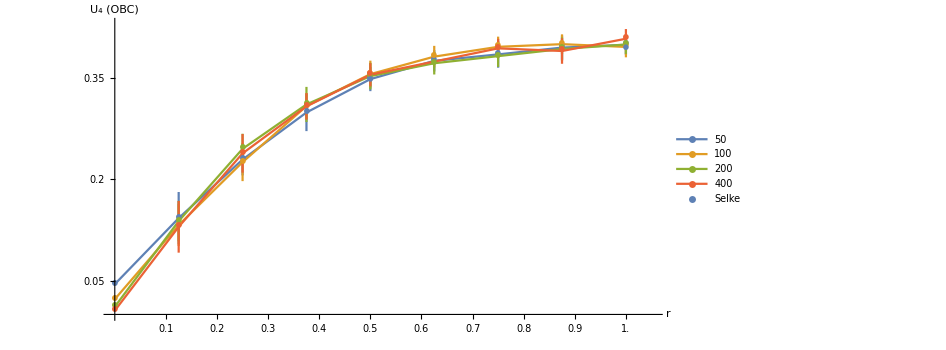

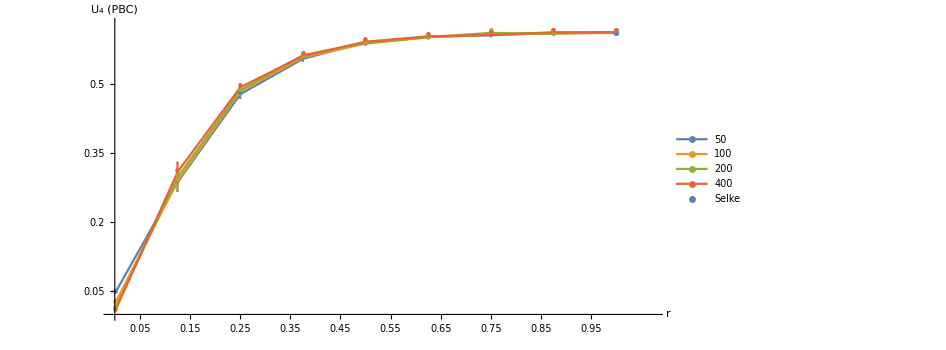

```mathematica
font=20;
Ls=Map[Style[#,font]&,{50,100,200,400}];
rOBC=ErrorListPlot[LinesOBC, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["r",FontSize->20], Style["U_4 (OBC)",FontSize->18]}, GridLines->{0.05*Range[20],0.05*Range[20]},Ticks->{0.1*Range[10],0.05*Range[20]},TicksStyle ->Directive[20], AspectRatio->0.5,PlotRange->{{0,1.05},{0,0.43}}];

rPBC=ErrorListPlot[LinesPBC, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,15}, AxesLabel->{Style["r",FontSize->20], Style["U_4 (PBC)",FontSize->18]}, GridLines->{0.05*Range[20],0.05*Range[20]},Ticks->{0.05*Range[20],0.05*Range[20]},TicksStyle ->Directive[13],AspectRatio->0.5,PlotRange->{{0.0,1.07},{0.00,0.63}}];

rTrueOBC=ListPlot[{{1/2, 0.349},{1,0.396}},PlotLegends->{Style["Selke",font]},PlotMarkers->{Style[♁, Black],25}];
rTruePBC=ListPlot[{{1,0.61069}},PlotLegends->{Style["Selke",font]},PlotMarkers->{Style[♁, Black],25}];
AllOBC=Show[rOBC,rTrueOBC]
AllPBC=Show[rPBC,rTruePBC]
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["CumulantOBC.png",AllOBC];
Export["CumulantPBC.png",AllPBC];
```

```mathematica
\[Fi
```

#### 17.04.2021 (Сравнение графиков W. Selke)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["resultsALL.txt","table"];
```

```mathematica
Ls={50,100,200,400};
```

```mathematica
dataOBC=Select[data, #[[3]]==1&];
```

```mathematica
dataPBC=Select[data,#[[3]]==0&];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
DotsForPlot2[data0_,Coef_]:=Module[{data=data0,Cs=Coef,FullData={},line={},dM2={},dM4={},dU4={},dot={},lData={}},
Needs["ErrorBarPlots`"];
Do[
lData=Sort[Select[data,#[[2]]==k&],#1[[1]]<#2[[1]]&];
	line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{1/lData[[i]][[1]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{k,Cs}];
Return[FullData];];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Coefs={0.125,0.25,0.375,0.5,0.625,0.75,0.875,1};
```

```mathematica
a=DotsForPlot2[dataOBC, Coefs]
```

```mathematica
a={{{{1/50,0.142698},ErrorBar[0.03804695563817599]},{{1/100,0.132452},ErrorBar[0.031605273821521264]},{{1/200,0.138382},ErrorBar[0.03034081299723745]},{{1/400,0.129828},ErrorBar[0.03911267995590849]}},{{{1/50,0.2295},ErrorBar[0.024170099986002027]},{{1/100,0.225718},ErrorBar[0.028880674045689]},{{1/200,0.245425},ErrorBar[0.023106285580623692]},{{1/400,0.238706},ErrorBar[0.029361146662440205]}},{{{1/50,0.299275},ErrorBar[0.028441878161144057]},{{1/100,0.308687},ErrorBar[0.019054483286967523]},{{1/200,0.31116},ErrorBar[0.024179256260963466]},{{1/400,0.30833},ErrorBar[0.018939662967785077]}},{{{1/50,0.348689},ErrorBar[0.018067210862038496]},{{1/100,0.356097},ErrorBar[0.019731531449266183]},{{1/200,0.353132},ErrorBar[0.020098316057156018]},{{1/400,0.355153},ErrorBar[0.016896097429090547]},{{0,0.349},ErrorBar[0.002]}},{{{1/50,0.375821},ErrorBar[0.01613552318127009]},{{1/100,0.382013},ErrorBar[0.01617066196336322]},{{1/200,0.372229},ErrorBar[0.01646741428802199]}},{{{1/50,0.385329},ErrorBar[0.0189546223474211]},{{1/100,0.396548},ErrorBar[0.015138200300344348]},{{1/200,0.382767},ErrorBar[0.016077902019022736]},{{1/400,0.394277},ErrorBar[0.014218301879383964]}},{{{1/50,0.395412},ErrorBar[0.017401966363986533]},{{1/100,0.40049},ErrorBar[0.01424451151613746]},{{1/200,0.39333},ErrorBar[0.01766771938687142]},{{1/400,0.390363},ErrorBar[0.019596643420068706]}},{{{1/50,0.399503},ErrorBar[0.014243984987823909]},{{1/100,0.396412},ErrorBar[0.015011106998929147]},{{1/200,0.400006},ErrorBar[0.01360823678267494]},{{1/400,0.40851539},ErrorBar[0.014266016729749918]},{{0,0.396},ErrorBar[0.002]}}};
```

```mathematica
t1={{1/50,1/50,{0.01,0}},{1/100,1/100,{0.01,0}},{1/200,1/200,{0.01,0}},{1/400,1/400,{0.01,0}}};
t2=Array[{#,Null,{0.005,0}}&,26,{0,0.025}];
t={Union[t1,t2],Automatic};
```

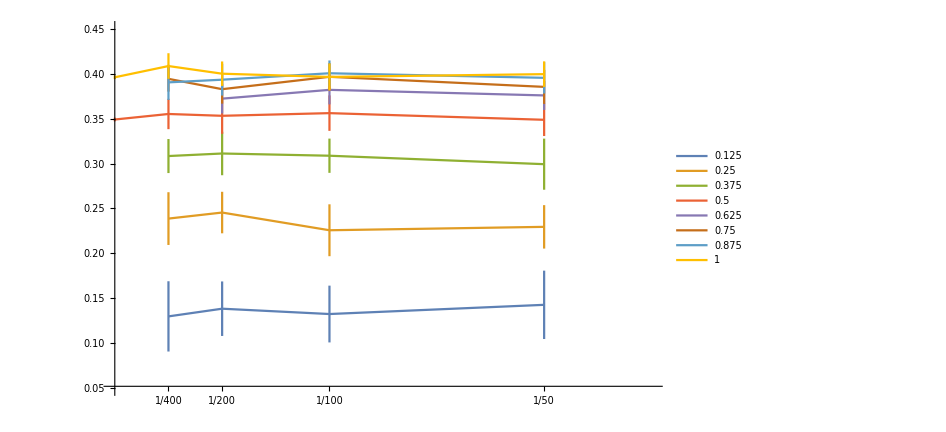

```mathematica
aOBC=ErrorListPlot[a,PlotLegends->Map[Style[#,17]&,Coefs],ImageSize->700,Joined->True,PlotRange->{{0,0.025},{0.05,0.45}},Ticks->t,TicksStyle->Directive["Label", 17]]
```

```mathematica
]
```

```mathematica
b=DotsForPlot2[dataPBC,Coefs]
```

```mathematica
b={{{{1/50,0.286747},ErrorBar[0.020309916502372013]},{{1/100,0.28937},ErrorBar[0.0187155906487972]},{{1/200,0.29759},ErrorBar[0.019687278464362797]},{{1/400,0.30893},ErrorBar[0.02228115197500553]}},{{{1/50,0.477888},ErrorBar[0.010186581042402295]},{{1/100,0.484009},ErrorBar[0.010600665466540638]},{{1/200,0.486162},ErrorBar[0.012037039018523233]},{{1/400,0.492787},ErrorBar[0.009072972684484407]}},{{{1/50,0.554871},ErrorBar[0.006370937869183853]},{{1/100,0.558207},ErrorBar[0.006187084720045908]},{{1/200,0.562739},ErrorBar[0.006620474101824917]},{{1/400,0.561456},ErrorBar[0.00937759741796361]}},{{{1/50,0.590986},ErrorBar[0.006414414184746243]},{{1/100,0.587857},ErrorBar[0.005290645833355218]},{{1/200,0.589294},ErrorBar[0.005815060905464715]},{{1/400,0.592052},ErrorBar[0.00576104064675085]}},{{{1/50,0.602755},ErrorBar[0.004296772897534279]},{{1/100,0.601601},ErrorBar[0.004633404076121194]},{{1/200,0.602077},ErrorBar[0.004769709564854037]},{{1/400,0.603632},ErrorBar[0.00437652114502106]}},{{{1/50,0.605987},ErrorBar[0.004429703977993762]},{{1/100,0.607562},ErrorBar[0.0049033100384293085]},{{1/200,0.611214},ErrorBar[0.003933104159964109]},{{1/400,0.606799},ErrorBar[0.0042113833041072714]}},{{{1/50,0.611505},ErrorBar[0.004040444200068307]},{{1/100,0.610132},ErrorBar[0.005157997027206836]},{{1/200,0.609289},ErrorBar[0.004793367222882582]},{{1/400,0.612557},ErrorBar[0.004261233193897928]}},{{{1/50,0.611031},ErrorBar[0.004190733149869287]},{{1/100,0.611278},ErrorBar[0.0042264563565317615]},{{1/200,0.612436},ErrorBar[0.004904990248018792]},{{1/400,0.612978},ErrorBar[0.004435798612785999]},{{0,0.61069},ErrorBar[0]}}}
```

{{{{1/50,0.286747},ErrorBar[0.0203099]},{{1/100,0.28937},ErrorBar[0.0187156]},{{1/200,0.29759},ErrorBar[0.0196873]},{{1/400,0.30893},ErrorBar[0.0222812]}},{{{1/50,0.477888},ErrorBar[0.0101866]},{{1/100,0.484009},ErrorBar[0.0106007]},{{1/200,0.486162},ErrorBar[0.012037]},{{1/400,0.492787},ErrorBar[0.00907297]}},{{{1/50,0.554871},ErrorBar[0.00637094]},{{1/100,0.558207},ErrorBar[0.00618708]},{{1/200,0.562739},ErrorBar[0.00662047]},{{1/400,0.561456},ErrorBar[0.0093776]}},{{{1/50,0.590986},ErrorBar[0.00641441]},{{1/100,0.587857},ErrorBar[0.00529065]},{{1/200,0.589294},ErrorBar[0.00581506]},{{1/400,0.592052},ErrorBar[0.00576104]}},{{{1/50,0.602755},ErrorBar[0.00429677]},{{1/100,0.601601},ErrorBar[0.0046334]},{{1/200,0.602077},ErrorBar[0.00476971]},{{1/400,0.603632},ErrorBar[0.00437652]}},{{{1/50,0.605987},ErrorBar[0.0044297]},{{1/100,0.607562},ErrorBar[0.00490331]},{{1/200,0.611214},ErrorBar[0.0039331]},{{1/400,0.606799},ErrorBar[0.00421138]}},{{{1/50,0.611505},ErrorBar[0.00404044]},{{1/100,0.610132},ErrorBar[0.005158]},{{1/200,0.609289},ErrorBar[0.00479337]},{{1/400,0.612557},ErrorBar[0.00426123]}},{{{1/50,0.611031},ErrorBar[0.00419073]},{{1/100,0.611278},ErrorBar[0.00422646]},{{1/200,0.612436},ErrorBar[0.00490499]},{{1/400,0.612978},ErrorBar[0.0044358]},{{0,0.61069},ErrorBar[0]}}}

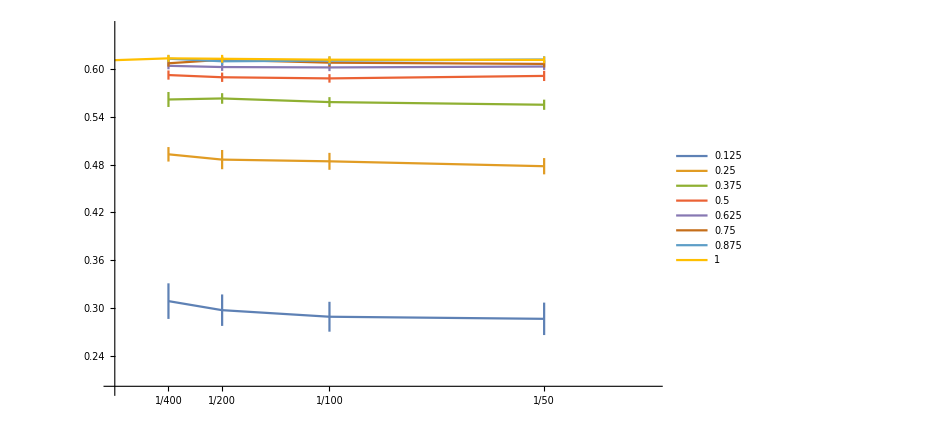

```mathematica
aPBC=ErrorListPlot[b,PlotLegends->Map[Style[#,17]&,Coefs],PlotRange->{{0,0.025},{0.2,0.65}},ImageSize->700,Joined->True,Ticks->t,TicksStyle->Directive["Label", 17]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["CumulantOBCL.png",aOBC];
Export["CumulantPBCL.png",aPBC];
```

```mathematica
trueOBC=ListPlot[{{0,0.396},{0,0.349}},PlotMarkers->{"-",40}];
truePBC=ListPlot[{{0,0.61069}},PlotMarkers->{"-",40}];
```

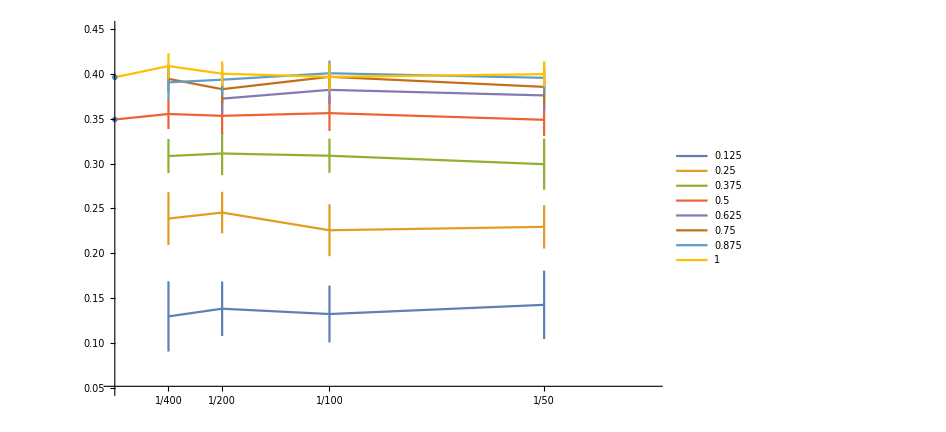

```mathematica
aOBC =Show[aOBC,trueOBC]
```

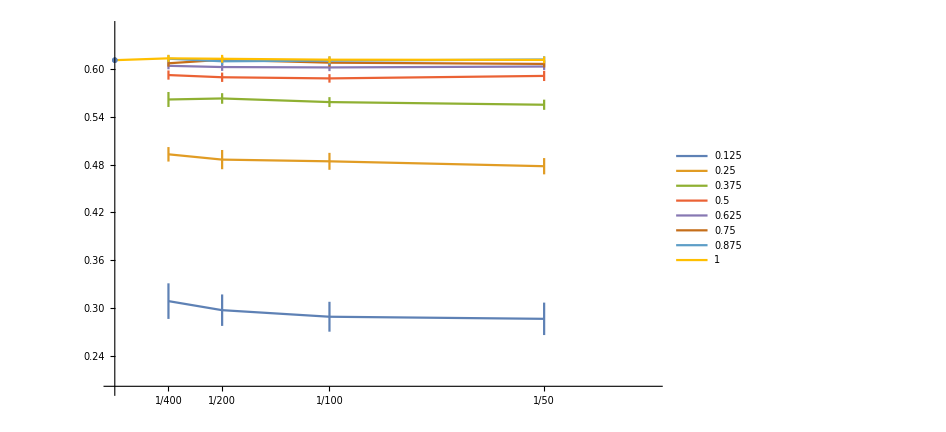

```mathematica
aPBC=Show[aPBC,truePBC]
```